Coherent state

```mathematica
ϕ[n_,α_]:=ⅇ^(-Abs[α]^2/2)α^n/(√(n!));
```

A useful function of gain

```mathematica
G[g_]:=(√(g^2-1))/g;
```

ACS (not normalized)

```mathematica
Psi[n_,α_,g_]:=ⅇ^(-Abs[G[g]α]^2/2)(1/g^2-n G[g]^2)ⅇ^(-Abs[α/g]^2/2)(α/g)^n/(√(n!));
```

Appropriate value of gain for the condition of zero overlap of ACS with the attenuated coherent state

```mathematica
g0[α_]:=1/(√(1-1/Abs[α]^2));
```

```mathematica
g1[α_]:=√((2-Abs[α]^2+√(Abs[α]^4+4))/2);
```

Norm of ACS

```mathematica
NormACS[α_,g_]:=(1/g^2-G[g]^2 Abs[α/g]^2)^2+G[g]^4 Abs[α/g]^2;
```

Probability of success (P_s)

```mathematica
Manipulate[Plot[ⅇ^(-Abs[G[g]α]^2)NormACS[α,g],{g,1,1.6},GridLines->{{{g0[α],Black},{g/.NSolve[g^4+(α^2-2)g^2-α^2==0&&g>1,{g}][[1]],Black},{g/.NSolve[Simplify[D[ⅇ^(-Abs[G[g]α]^2)NormACS[α,g],g]]==0&&g>1&&Element[g,Reals],g][[2]],Black}},{.02}},PlotRange->Full,AxesOrigin->{1,0},AxesLabel->{"g","P_s"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}],{α,2,10,1}]
```

```mathematica
InnerProductPACS[α_,g_]:=((α/g)/(√(Abs[α/g]^2+1))(1/g^2-G[g]^2(Abs[α/g]^2+1)))/(√NormACS[α,g]);
InnerProductDFS[α_,g_]:=(G[g]^2 α/g)/(√NormACS[α,g]);
InnerProductCS[α_,g_]:=(1/g^2-Abs[α/g]^2 G[g]^2)/(√NormACS[α,g]);
```

Plot showing contributions of the attenuated coherent state and the photon added coherent state to the final state as a function of gain value

```mathematica
FullSimplify[(G[g1[A]]^2 A/g1[A])/(√NormACS[A,g1[A]])]
```

(A (√(4+Abs[A]^4)-A Conjugate[A]) √(2+Abs[A]^4-√(4+Abs[A]^4)+Abs[A]^2 √(4+Abs[A]^4)-A Conjugate[A]))/(2 √2 Abs[A])

```mathematica
FullSimplify[(1/g1[A]^2-G[g1[A]]^2 Abs[A/g1[A]]^2)]
```

(2 (2+Abs[A]^4+√(4+Abs[A]^4)-A (1+√(4+Abs[A]^4)) Conjugate[A]))/((2+√(4+Abs[A]^4)-A Conjugate[A])^2)

```mathematica
Manipulate[Plot[{(InnerProductDFS[α,ⅇ^(sqlogg^4)])^2,(InnerProductCS[α,ⅇ^(sqlogg^4)])^2,(InnerProductPACS[α,ⅇ^(sqlogg^4)])^2},{sqlogg,0,1.2},AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Gray,Black,{Black,Dashed}},AxesLabel->{"(ln (g))^(1/4)","|C|^2"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"DFS","CS","PACS"}],{α,1.01,7}]
```

Normalized ACS

```mathematica
ψ[n_,α_,g_]:=((1/g^2-n G[g]^2)ⅇ^(-Abs[α/g]^2/2)(α/g)^n/(√(n!)))/(√NormACS[α,g]);
```

Checking that the total probability adds up to 1

```mathematica
∑_(n=0)^∞ N[ψ[n,√10,g0[√10]]]^2
```

1.

```mathematica
CoefficientOfCoherentState[α_,g_]:=(1/g^2)/(√NormACS[α,g]);
CoefficientOfPhotonAddedState[α_,g_]:=-(α/g G[g]^2 √(Abs[α/g]^2+1))/(√NormACS[α,g]);
```

```mathematica
Manipulate[Plot[{CoefficientOfCoherentState[α,ⅇ^(x^4)],CoefficientOfPhotonAddedState[α,ⅇ^(x^4)]},{x,0,1.2},AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Gray,Black},AxesLabel->{"(ln (g))^(1/4)","C"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"Coherent","Photon Added"}],{α,1.01,7}]
```

Plot of required value of gain to create ACS as a function of average photon number of the original (unattenuated) coherent state

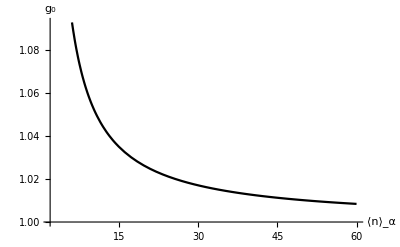

```mathematica
Plot[g0[√navg0],{navg0,2,60},AxesOrigin->{2,1},AxesLabel->{"⟨n⟩_α","g_0"},PlotStyle->{Black},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}]
```

Plot of attenuated coherent state and corresponding ACS for different values of average photon number for the original (unattenuated) coherent state

```mathematica
navg0=16;
```

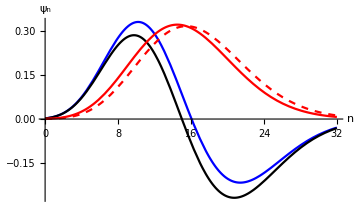

```mathematica
Plot[{ψ[n,√navg0,g1[√navg0]],ψ[n,√navg0,g0[√navg0]],ϕ[n,(√navg0)/g0[√navg0]],ϕ[n,√navg0]},{n,0,2navg0},PlotRange->Full,PlotStyle->{Blue,Black,Red,{Red,Dashed}},AxesLabel->{"n","ψ_n"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}]
```

```mathematica
Manipulate[Plot[{ψ[n,√navg0,g],ϕ[n,(√navg0)/g]},{n,0,2navg0},PlotRange->Full,AxesOrigin->{0,0}],{g,1,1.25g0[√navg0]}]
```

Wigner function of coherent state

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ 1/π^2 ⅇ^((x-ⅈ y)(a+ⅈ b)-(x+ⅈ y)(a-ⅈ b)-(x^2+y^2)/2)ⅆxⅆy
```

(2 ⅇ^(-2 (a^2+b^2)))/π

```mathematica
Wc[β_,a_,b_]:=(2 ⅇ^(-2 Abs[(a+ⅈ b)-β]^2))/π;
Manipulate[ContourPlot[Wc[√navg0,a,b],{a,√navg0-2.5,√navg0+2.5},{b,-2.5,2.5},PlotRange->Full,GridLines->Automatic,Contours->3,PlotLegends->Automatic],{navg0,3,100,1}]
```

Wigner function of one photon added coherent state

```mathematica
Wc1[β_,a_,b_]:=((Abs[2(a+ⅈ b)-β/g0[β]]^2-1)/(Abs[β/g0[β]]^2+1))(2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g0[β]]^2))/π;
```

Checking that the integral of the Wigner function gives 1

```mathematica
(*N[∫_(-∞)^∞ ∫_(-∞)^∞ Wc1[√navg0,a,b]ⅆaⅆb]*)
```

```mathematica
Manipulate[ContourPlot[Wc1[√navg0,a,b],{a,√navg0-4,√navg0+4},{b,-4,4},PlotRange->Full,PlotLegends->Automatic,GridLines->Automatic,Contours->5],{navg0,1.1,2}]
```

### Plot along the real axis

```mathematica
Manipulate[Plot[Wc1[√navg0,a,0],{a,√navg0-5,√navg0+5},PlotRange->Full,PlotLegends->Automatic,GridLines->Automatic],{navg0,1.1,2}]
```

Calculations to simplify the third term in the Wigner function of ACS

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ (x+ⅈ y)/π^2 ⅇ^((x-ⅈ y)(a+ⅈ b)-(x+ⅈ y)(a-ⅈ b)-(x^2+y^2)/2)ⅆxⅆy
```

(4 (a+ⅈ b) ⅇ^(-2 (a^2+b^2)))/π

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ (x-ⅈ y)/π^2 ⅇ^((x-ⅈ y)(a+ⅈ b)-(x+ⅈ y)(a-ⅈ b)-(x^2+y^2)/2)ⅆxⅆy
```

-(4 (a-ⅈ b) ⅇ^(-2 (a^2+b^2)))/π

Wigner function of ACS

```mathematica
navg0=6;
```

```mathematica
W[β_,a_,b_]:=1/NormACS[β,g0[β]](1/g0[β]^4+2/g0[β]^2 G[g0[β]]^2 Abs[β/g0[β]]^2+G[g0[β]]^4 Abs[β/g0[β]]^2(Abs[2(a+ⅈ b)-β/g0[β]]^2-1)-2/g0[β]^3 G[g0[β]]^2(β*(a+ⅈ b)+(a-ⅈ b)β))(2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g0[β]]^2))/π;
```

```mathematica
Term1[β_,a_,b_]:=((2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g0[β]]^2))/π)/(g0[β]^4 NormACS[β,g0[β]]);
Term2[β_,a_,b_]:=(G[g0[β]]^4 Abs[β/g0[β]]^2(Abs[2(a+ⅈ b)-β/g0[β]]^2-1)(2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g0[β]]^2))/π)/NormACS[β,g0[β]];
Term3[β_,a_,b_]:=((2/g0[β]^2 G[g0[β]]^2 Abs[β/g0[β]]^2-2/g0[β]^3 G[g0[β]]^2(β*(a+ⅈ b)+(a-ⅈ b)β))(2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g0[β]]^2))/π)/NormACS[β,g0[β]];
```

```mathematica
Manipulate[Plot3D[W[√navg0,a,b],{a,√navg0-2,√navg0+2},{b,-2,2},PlotRange->Full,PlotLegends->Automatic],{navg0,1.1,10}]
```

```mathematica
DynamicModule[{navg0=9},Plot3D[W[√navg0,a,b],{a,√navg0-2,√navg0+2},{b,-2,2},PlotRange->Full,PlotLegends->Automatic]]
```

Checking that the integral of the Wigner function gives 1

```mathematica
(*∫_(-∞)^∞ ∫_(-∞)^∞ W[√navg0,a,b]ⅆaⅆb*)
```

### Plot along the real axis

```mathematica
Manipulate[Plot[W[√navg0,a,0],{a,√navg0-2.5,√navg0+2.5},PlotRange->Full],{navg0,3,100.1}]
```

Wigner function of Displaced one photon number state

```mathematica
Manipulate[ContourPlot[WdN[(√navg0)/g0[√navg0],a,b],{a,√navg0-5,√navg0+5},{b,-5,5},PlotRange->Full,PlotLegends->Automatic,GridLines->Automatic,Contours->5],{navg0,3,100,1}]
```

```mathematica
WdN[β_,a_,b_]:=-(-4 Abs[(a+ⅈ b)-β]^2+1)(2 ⅇ^(-2 Abs[(a+ⅈ b)-β]^2))/π
```

Difference between Wigner function of ACDS and 1 photon displaced state

```mathematica
FullSimplify[W[√navg0,a,b]-WdN[(√navg0)/g0[√navg0],a,b],Element[a,Reals]&&Element[b,Reals]]
```

0

```mathematica
Manipulate[Plot[{W[√navg0,a,0],WdN[(√navg0)/g0[√navg0],a,0]},{a,√navg0-2.5,√navg0+2.5},PlotRange->Full,PlotStyle->{Dashed,Dotted},PlotLegends->Automatic],{navg0,3,100,1}]
```

```mathematica
Manipulate[Plot[{Term1[√navg0,a,0],Term2[√navg0,a,0],Term3[√navg0,a,0]},{a,√navg0-2.5,√navg0+2.5},PlotRange->Full,PlotLegends->Automatic],{navg0,3,100,1}]
```

```mathematica
Manipulate[Plot[{Term1[√navg0,a,0]+Term2[√navg0,a,0]+Term3[√navg0,a,0]},{a,√navg0-2.5,√navg0+2.5},PlotRange->Full,PlotLegends->Automatic],{navg0,3,100,1}]
```